This file contains functions used by ERACS to plot the pareto front.

# Functions

```mathematica
<<".mathrc";
```

```mathematica
colorData = ColorData[3];
```

```mathematica
dpi = 72;
```

```mathematica
myMarkerSize = .4 dpi;
```

```mathematica
circle[] := Graphics[Circle[], ImageSize -> myMarkerSize]
```

```mathematica
box[] := Graphics[{EdgeForm[Black], Transparent, Rectangle[]}, ImageSize->myMarkerSize]
```

```mathematica
plotFront[points_, index_:1] := Module[{p1, p2, p3},
p1 = ListPlot[points, Joined ->True, PlotLegends -> LineLegend[{"front"}], PlotRangePadding -> Scaled[.1]];
p2 = ListPlot[Map[List, points], PlotStyle -> Map[colorData, Range[Length[points]]],
PlotMarkers -> {Automatic, Medium}, PlotLegends -> Map[ToString,Range[Length[points]]]];
p3 = ListPlot[{points[[index]]},
PlotMarkers -> {circle[]}, PlotLegends -> {"current"}, PlotStyle -> Black];
Show[p1,p2, p3]]
```

```mathematica
plotPoint[point_, opts:OptionsPattern[Options[ListPlot]]] := ListPlot[{point},PlotMarkers -> {Automatic, Medium}, Evaluate[FilterRules[{opts},Options[ListPlot]]]]
```

```mathematica
plotFrontAndPoint[points_, index_, lastPoint_] :=
Show[{plotFront[points, index], plotPoint[lastPoint, PlotLegends ->{"previous"}, PlotStyle -> {colorData[ 1+Length[points]]}]}, PlotRange -> All]
```

```mathematica
exportPDF[filename_, expr_] := Export[filename, expr,"PDF"(*, ImageSize ->10 inches*)]
```

```mathematica
mathematicaToSexp[x_RGBColor] := ("#"<>mathematicaToSexp[Apply[List,Append[x,1.]]])
```

```mathematica
mathematicaToSexp[x_List] := ("(" <> StringJoin[Riffle[Map[mathematicaToSexp,x], " "]]<> ")")
```

```mathematica
mathematicaToSexp[x_Real] := ToString[x]
```

```mathematica
mathematicaToSexp[x_Integer] := ToString[x]
```

```mathematica
path[{}] := {}
```

```mathematica
path[points_] := Line[points]
```

```mathematica
box[pos_, dims_] := {Transparent, Cuboid[pos - dims/2, pos + dims/2]}
```

```mathematica
plotRobotPathAndObstacles[points_, obstacles_, ind_:1,opts:OptionsPattern[Graphics3D]] :=
Graphics3D[{{colorData[ind],path[points]}, Map[box@@#&,obstacles], 
If[Length[points] > 0,{{PointSize[Large],Green, Opacity[0.5], Point[points[[-1]]]},
{PointSize[Large],Red, Opacity[0.5], Point[points[[1]]]}},
{}]
},
Evaluate[FilterRules[{opts},Options[Graphics3D]]],Axes->{True, False, True},AxesLabel->{"x","y","z"},ViewPoint->{0,Infinity,0},ViewVertical->{0,0,-1}, PlotRangePadding -> 2, ImageSize -> pdfImageSize]
```

```mathematica
boxyCylinder[radius_, length_, axis_] := Module[{dims}, dims = {1,1,1} radius * 2;
dims[[axis]] = length;
dims]
```

```mathematica
plotScene[] := Module[{target, wall, body,legs},
wall = {{0, 1, -5}, {10, 1, 1}};
target = {{0,1,-10}, {1,1,1}};
body = {{0,1,0}, {1,.2,1}};
legs = {{{1,1,0},{0.1,1,1}},{{1.5,0.5,0},{0.1,1,2}},{{0,1,-1},{0.1,1,3}},{{0,0.5,-1.5},{0.1,1,2}},{{-1,1,0},{0.1,1,1}},{{-1.5,0.5,0},{0.1,1,2}},{{0,1,1},{0.1,1,3}},{{0,0.5,1.5},{0.1,1,2}}};
plotRobotPathAndObstacles[{}, {wall,target, body, Sequence@@Map[{#[[1]], boxyCylinder@@#[[2]]}&, legs]},1, ImageSize -> Automatic]]
```

```mathematica
plotRobotPathAndObstaclesSideView[args__] :=
plotRobotPathAndObstacles@@{args}~Join~{ViewPoint -> {Infinity, 0, 0}, ViewVertical -> {0,1,0}(*ViewAngle -> 3 Degree, ViewRange -> {0, 10}*),Axes -> {False, True, True}}
```

```mathematica
plotRobotPathAndObstaclesTwoViews[args__] :=
GraphicsGrid[{{plotRobotPathAndObstacles@@{args}~Join~{ImageSize -> Automatic}, plotRobotPathAndObstaclesSideView@@{args}~Join~{ImageSize -> Automatic}}}, ImageSize -> pdfImageSize]
```

```mathematica
(*plotRobotPathWithJump[points_,target_, ditchWidth_, ditchDepth_, ind_:1, opts:OptionsPattern[Graphics3D]] :=
Module[{bodySize = 4.},
Graphics3D[{{colorData[ind],path[points]}, 
box[target - {0,0,1} ditchWidth,{1,1,1}],
box[{0,-ditchDepth/2, -ditchWidth/2 - bodySize /4},{10,ditchDepth, ditchWidth}], 
(* robot *)
box[{0,1,0}, {1,1,1} bodySize/2], {PointSize[Large],Green, Opacity[0.5], Point[points[[-1]]]},
{PointSize[Large],Red, Opacity[0.5], Point[points[[1]]]}},Evaluate[FilterRules[{opts},Options[Graphics3D]],Axes->{True, False, True},AxesLabel->{"x","y","z"},ViewPoint->{0,Infinity,0},ViewVertical->{0,0,-1} (*PlotRangePadding -> 2,*) PlotRange -> 10 ]]]*)
```

```mathematica
plotFitnessTimeSeries[results_, opts:OptionsPattern[Options[ListPlot]]] := ListPlot[Transpose[Map[Function[{input}, Map[ {input[[1]], #}&,input[[2]]]],results[[All,{1,3}]]]],Evaluate[FilterRules[{opts},Options[ListPlot]]], Joined -> False, PlotRange -> All, AxesLabel -> {"generation", "fitness"}, AxesOrigin -> {1, 0}, Evaluate[FilterRules[{opts}, Options[ListPlot]]]]
```

# Demo

```mathematica
Dynamic[plotScene[]]
```

```mathematica
jumpObstacles = {{{0.0,-10.0,-30.0},{50.0,20.0,50.0}},{{0.0,-13.0,0.0},{50.0,20.0,50.0}},{{0.0,-10.0,23.0},{50.0,20.0,50.0}}};
```

```mathematica
jumpObstacles = {{{0.0,-1.5,-15.0},{20.0,3.0,20.0}},{{0.0,-4.5,-4.0},{20.0,3.0,43.0}},{{0.0,-1.5,8.0},{20.0,3.0,20.0}}};
```

```mathematica
jumpObstacles = {{{0.0,-1.5,-15.0},{20.0,3.0,20.0}},{{0.0,-4.5,-3.5},{20.0,3.0,43.0}},{{0.0,-1.5,8.0},{20.0,3.0,20.0}}};
```

```mathematica
a /. {a -> 1, a -> 2}
```

1

```mathematica
Dynamic[plotRobotPathWithJump[Reverse[{{0,1,0}, {0,1,-1}}], {0, 4, -3}, 2, 3, 4, ViewPoint -> {Infinity, 0, 0}, ViewVertical -> {0,1,0}, Axes -> {False, True, True}]]
```

```mathematica
Dynamic[plotRobotPathAndObstacles[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4, ViewPoint -> {Infinity, 0, 0}, ViewVertical -> {0,1,0}(*ViewAngle -> 3 Degree, ViewRange -> {0, 10}*),Axes -> {False, True, True}]]
```

```mathematica
Dynamic[plotRobotPathAndObstacles[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4]]
```

```mathematica
Dynamic[plotRobotPathAndObstaclesSideView[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4]]
```

```mathematica
Dynamic[GraphicsGrid[{{plotRobotPathAndObstacles[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4], plotRobotPathAndObstaclesSideView[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4]}}]]
```

```mathematica
Export["blah.pdf", %180, ImageSize -> Large]
```

blah.pdf

```mathematica
SystemOpen["blah.pdf"]
```

```mathematica
SystemOpen["blah.pdf"]
```

```mathematica
SystemOpen["blah.pdf"]
```

```mathematica
SystemOpen["blah.pdf"]
```

```mathematica
SystemOpen["blah.pdf"]
```

```mathematica
Dynamic[plotRobotPathAndObstaclesTwoViews[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4]]
```

```mathematica
Dynamic[Graphics3D[{path[{{1,1,-1},{2,2,1},{3,3,-1},{4,4,1}}],
box[{0,0,0}, {1,1,1}]}, Axes -> {True, False, True}, AxesLabel -> {"x", "y", "z"}]]
```

```mathematica
exportPDF["path-plot.pdf",Graphics3D[{path[{{-0.0253487136214972,1.00817763805389,0.181168854236603},{-0.0161291677504778,1.02566242218018,0.172572240233421},{-0.00676033133640885,1.04400062561035,0.163045942783356},{0.00324325961992145,1.0616934299469,0.151699468493462},{0.011848384514451,1.0788494348526,0.138777449727058},{0.0178895760327578,1.09289968013763,0.123955070972443},{0.0204286016523838,1.10191190242767,0.105577759444714},{0.0362350679934025,1.16575658321381,0.0971855372190475},{0.0508939176797867,1.25194191932678,0.0840362086892128},{0.0466832369565964,1.31302404403687,0.0638626888394356},{0.0188884176313877,1.34766161441803,0.0156778674572706},{-0.00405020080506802,1.20635282993317,-0.0148862600326538}}]},Axes->True,AxesLabel->{"x","y","z"}]]
```

```mathematica
exportPDF["test.pdf", Graphics3D[{path[{{1,1,-1},{2,2,1},{3,3,-1},{4,4,1}}],
box[{0,0,0}, {1,1,1}]}, Axes -> True, AxesLabel -> {"x", "y", "z"}]]
```

test.pdf

```mathematica
SystemOpen["test.pdf"]
```

```mathematica
SetDirectory["/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs"];
```

```mathematica
exportColorData[filename_] := Export[filename,"(define colors #"<>mathematicaToSexp[Map[colorData, Range[10]]] <> ")", "Text"]
```

```mathematica
"what" >> "colors.scm"
```

```mathematica
exportColorData["colors.scm"];
```

```mathematica
Directory[]
```

/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs

```mathematica
mathematicaToSexp[Map[colorData, Range[10]]]//FullForm
```

"(#(0. 0. 0. 1.) #(0.996078 0.360784 0.027451 1.) #(0.996078 0.988235 0.0352941 1.) #(0.541176 0.713725 0.027451 1.) #(0.145098 0.435294 0.384314 1.) #(0.00784314 0.509804 0.929412 1.) #(0.152941 0.113725 0.490196 1.) #(0.470588 0.262745 0.584314 1.) #(0.890196 0.0117647 0.490196 1.) #(0.905882 0.027451 0.129412 1.))"

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
testFront
```

{{10,20},{30,60},{50,90}}

```mathematica
Dynamic[Show[plotFrontAndPoint[testFront, 2, -10 {-1,-1}], AxesLabel -> {"hi", "bye"}, AxesOrigin -> {0, 0}]]
```

```mathematica
Dynamic[plotPoint[{1,3}]]
```

```mathematica
testFront = 10{{1, 2}, {3,6}, {5, 9}}
```

{{10,20},{30,60},{50,90}}

```mathematica
Dynamic[plotFront[testFront, 3]]
```

```mathematica
Dynamic[Show[plotFront[testFront], AxesLabel -> {"hi", "bye"}]]
```

```mathematica
results = Import["run2/exp1-trial1/results.m"]
```

{{{1,12,{-0.0247998}},{1,2,{-0.211763}},{1,4,{-0.121844}},{1,3,{-0.153889}},{1,11,{-0.0298947}},{1,9,{-0.0517239}},{1,8,{-0.0578939}},{1,1,{-0.231577}},{1,6,{-0.0766132}},{1,10,{-0.0453977}},{1,5,{-0.110337}},{1,7,{-0.0649858}}},«98»,{{100,1,{-0.371371}},{100,1,{-0.371371}},{100,1,{-0.371371}},{100,1,{-0.371371}},«5»,{100,1,{-0.371371}},{100,1,{-0.371371}},{100,1,{-0.371371}}}}

```mathematica
results2 = {{{1, 1, {1, 2}}}, {{10, 2, {3, 5}}}}
```

{{{1,1,{1,2}}},{{10,2,{3,5}}}}

```mathematica
Transpose[Map[Function[{input}, Map[ {input[[1]], #}&,input[[2]]]],Flatten[results2,1][[All,{1,3}]]]]
```

{{{1,1},{10,3}},{{1,2},{10,5}}}

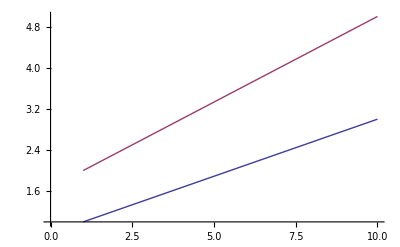

```mathematica
ListPlot[%99, Joined -> True]
```

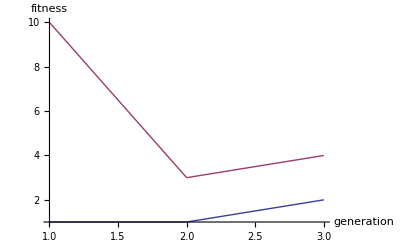

```mathematica
ListPlot[Map[{#[[1]], Sequence@@#[[2]]}&,Flatten[results2,1][[All,{1,3}]]], Joined -> True, PlotRange -> All, AxesLabel -> {"generation", "fitness"}]
```

```mathematica
(* sdf *)
```

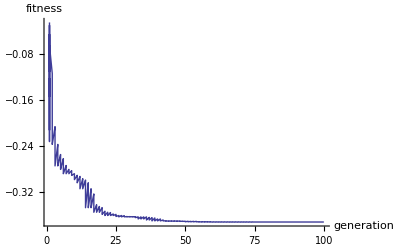

```mathematica
plotFitnessTimeSeries[Flatten[results,1]]
```

```mathematica
results3 = {{2,1,{-0.118770812499568}},{2,2,{-0.0859484364250073}},{2,3,{-0.0821600600881641}},{2,4,{-0.0745411813687041}},{1,3,{-0.0591417080332803}},{1,4,{-0.038307546587095}},{1,1,{-0.0859484364250073}},{1,2,{-0.0745411813687041}}};
```

```mathematica
?BarChart
```

BarChart[{y_1,y_2,…}] makes a bar chart with bar lengths y_1,  y_2, … .
BarChart[{…,w_i[y_i,…],…,w_j[y_j,…],…}] makes a bar chart with bar features defined by the symbolic wrappers w_k.
BarChart[{data_1,data_2,…}] makes a bar chart from multiple datasets data_i.

```mathematica
<<shane`
```

```mathematica
length[{1,2,3}]
```

3

```mathematica
chunk[x_,chunkSize_]:=Floor[x/chunkSize] chunkSize
```

```mathematica
chunk[1.1, 1]
```

1

```mathematica
makePairwiseLabel[p1_, p2_,ymax_, text_, scaled_:0.05] :=
{Line[{Scaled[{0, scaled},p1],
{p1[[1]], ymax}, 
{p2[[1]], ymax},
Scaled[{0, scaled},p2]}],
Text[text, 
{(p1[[1]] + p2[[1]])/2, ymax}, 
{0,-1}]}
```

```mathematica
composePairwiseLabels[positions_, labels_] := Module[{f},
MapThread[(f[#1] = #2)&, {Range[1,Length[positions]], positions}];
Map[Module[{p1, p2,label,args},
args = #;
p1 = f[args[[1]]];
p2 = f[args[[2]]];
label = makePairwiseLabel@@{p1, p2}~Join~args[[3;;-1]];
f[args[[1]]] = {p1[[1]], args[[3]]};
f[args[[2]]] = {p2[[1]], args[[3]]};
label]&,labels]]
```

```mathematica
{1,2,3,4}[[2;;-1]]
```

{2,3,4}

```mathematica
Clear[makePairwiseLabel]
```

```mathematica
Dynamic[barChartWithSEM[{1,3,4}, 0{1,1,.5}, pairwiseLabels -> Reverse@{{1,2, 6, "hi"},
{2,3, 5, "what?"}}, PlotRangePadding -> {{0,0}, {0, 3}}]]
```

```mathematica
barWithStandardError[{{xmin_,xmax_},{ymin_,ymax_}},y_,data_]:=Module[{xmed,SE,maxMean, text, number,r},
(*Print[{xmin, xmax}, {ymin, ymax}, y, data];*)
xmed=Mean[{xmin,xmax}];
SE=data[[1,1]];
text = data[[1,2]];
maxMean=data[[1,3]];
number = data[[1,4]];
r = data[[1,5]];
r[number] = {xmed, ymax + SE};
{{Black,
Line[{{xmin,ymax+SE},{xmax,ymax+SE}}],Line[{{xmed,ymax},{xmed,ymax+SE}}],
Text[text,
{xmed,ymax+SE}, {0, -1}]},
Rectangle[{xmin,ymin},{xmax,ymax}]}]
```

```mathematica
myAxesLabel[{labelx_,labely_},offset_:{0,0}]:=Sequence[PlotRangeClipping->False,ImagePadding->{{Scaled[.11-.5 offset[[2]]],Automatic},{Scaled[.09-offset[[1]]],Automatic}},Epilog->{Text[Rotate[axesLabel[labelx],0],Scaled[{.5,-.20+offset[[1]]}]],Text[Rotate[axesLabel[labely],Pi/2],Scaled[{-.15+offset[[2]],.5}]]}]
```

```mathematica
axesLabel[str_]:=label[str,15];
titleLabel[str_]:=label[str,18];
label[str_,size_:13]:=Style[str,size];
SetAttributes[label,Listable];
```

```mathematica
pairwiseLabels = pairwiseLabels;
Options[barChartWithSEM]={pairwiseLabels -> None}~Join~Options[BarChart];
```

```mathematica
Dynamic[barChartWithSEM[{1, 3}, {1, 1}, Epilog ->{makePairwiseLabel[{1,2}, {2,4},5, "**"]}, PlotRangePadding -> {{0,0},{0, 2}}]]
```

```mathematica
barChartWithSEM[data_, opt:OptionsPattern[]] :=
barChartWithSEM[Map[Mean, data], Map[standardErrorOfMean, data], Evaluate[opt]]
```

```mathematica
barChartWithSEM[means_, sems_, opt:OptionsPattern[]] := 
Module[{metadata, maxMean, positions},
maxMean = Max[means];
metadata = MapThread[List[#1,"", maxMean, #2, positions]&, {sems, Range[1, Length[sems]]}];
BarChart[MapThread[Rule, {means, metadata}],Evaluate[FilterRules[{opt},Options[BarChart]]],
ChartElementFunction->barWithStandardError, Epilog -> If[OptionValue[pairwiseLabels] =!= None,
composePairwiseLabels[Map[positions, Range[1, Length[sems]]],
OptionValue[pairwiseLabels]], {}]
]]
```

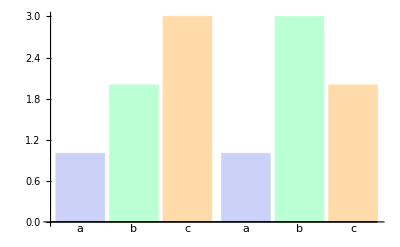

```mathematica
BarChart[{{1,2,3},{1,3,2}},ChartLabels->{"a","b","c"}(*, ChartElementFunction -> barWithStandardError*)]
```

```mathematica
(*
Matrix looks like this:
                control       AP
   success
failure 
*)
```

```mathematica
proportionsToMatrix[{p1_, n1_}, {p2_, n2_}] := 
{{p1 n1, p2 n2},
{(1 - p1) n1, (1 - p2)n2}}
```

```mathematica
results10 = {{.4, 10}, {1, 10}, {.6,10}, {.5, 10}, {1,10}, {.7, 10}};
```

```mathematica
control = {1/3, 30};
ap = {0.9, 30};
apPassive = {.5333, 30};
hlwpa1 = {.5484, 30};
hlwpa3 = {.8, 30};
hlwpa5 = {.7333,30};
results30 = {control, ap, apPassive, hlwpa1, hlwpa3, hlwpa5};
```

```mathematica
resultsNames = {"control", "AP", "APpassive", "WP a=.1", "WP a=.3", "WP a=.5"};
```

```mathematica
calcSignificance[results_] := Module[{f,n},
f[a_, b_] := fischerExactTest@Round@proportionsToMatrix[a, b];
n = Length[results];
Array[If[#1 < #2,
f[results[[#1]], results[[#2]]],
f[results[[#2]], results[[#1]]]]&, {n, n}]
]
```

```mathematica
sigs30 = calcSignificance[results30]
```

```mathematica
sigs10 = calcSignificance[results10];
```

```mathematica
sigs30 //N // mf
```

(1. | 0.0000109799 | 0.192317 | 0.192317 | 0.000573726 | 0.00402546
0.0000109799 | 1. | 0.00342116 | 0.00342116 | 0.471645 | 0.18058
0.192317 | 0.00342116 | 1. | 1. | 0.0538972 | 0.179869
0.192317 | 0.00342116 | 1. | 1. | 0.0538972 | 0.179869
0.000573726 | 0.471645 | 0.0538972 | 0.0538972 | 1. | 0.761068
0.00402546 | 0.18058 | 0.179869 | 0.179869 | 0.761068 | 1.)

```mathematica
sigToStars[sigs30] //mf
```

```mathematica
stars10 = sigToStars[sigs10]
```

{{,*,,,*,},{*,,,*,,},{,,,,,},{,*,,,*,},{*,,,*,,},{,,,,,}}

```mathematica
stars30 = %376;
```

```mathematica
TableForm[stars30, TableHeadings -> {resultsNames, resultsNames}]
```

| control | AP | APpassive | WP a=.1 | WP a=.3 | WP a=.5
control |  | *** |  |  | *** | **
AP | *** |  | ** | ** |  | 
APpassive |  | ** |  |  |  | 
WP a=.1 |  | ** |  |  |  | 
WP a=.3 | *** |  |  |  |  | 
WP a=.5 | ** |  |  |  |  |

```mathematica
makeRoughLabels[starsArray_] := Module[{A},
Reap[Array[If[#1 < #2 && starsArray[[#1, #2]] =!= "",
Sow[{#1, #2,1, starsArray[[#1, #2]]}]
None]&, Dimensions[starsArray]]][[2,1]]
]
```

```mathematica
makeRoughLabels[stars30]
```

{{1,2,1,***},{1,5,1,***},{1,6,1,**},{2,3,1,**},{2,4,1,**}}

```mathematica
TableForm[stars10, TableHeadings -> {resultsNames, resultsNames}]
```

| control | AP | APpassive | WP a=.1 | WP a=.3 | WP a=.5
control |  | * |  |  | * | 
AP | * |  |  | * |  | 
APpassive |  |  |  |  |  | 
WP a=.1 |  | * |  |  | * | 
WP a=.3 | * |  |  | * |  | 
WP a=.5 |  |  |  |  |  |

```mathematica
?TableForm
```

TableForm[list] prints with the elements of list arranged in an array of rectangular cells.

```mathematica
Round[proportionsToMatrix[1/3, 30, .9, 30]]
```

{{10,27},{20,3}}

```mathematica
?BernoulliDistribution
```

BernoulliDistribution[p] represents a Bernoulli distribution with probability parameter p.

```mathematica
sampleStandardDeviation[BinomialDistribution[n, p]]
```

√(n (1-p) p)

```mathematica
standardErrorOfMean[BinomialDistribution[30, .5]]
```

0.5

```mathematica
controlvsAP = %127
```

{{10,27},{20,3}}

```mathematica
controlvsAPpassive = Round[proportionsToMatrix[1/3,30,0.5333, 30]]
```

{{10,16},{20,14}}

```mathematica
apvsAPpassive = Round[proportionsToMatrix[.9, 30, 0.5333, 30]]
```

{{27,16},{3,14}}

```mathematica
fischerExactTest[controlvsAP]
```

378379/34461144151

```mathematica
?Array
```

Array[f,n] generates a list of length n, with elements f[i]. 
Array[f,n,r] generates a list using the index origin r.
Array[f,n,{a,b}] generates a list using n values from a to b.
Array[f,{n_1,n_2,…}] generates an n_1×n_2×… array of nested lists, with elements f[i_1,i_2,…]. 
Array[f,{n_1,n_2,…},{r_1,r_2,…}] generates a list using the index origins r_i (default 1). 
Array[f,{n_1,n_2,…},{{a_1,b_1},{a_2,b_2},…}] generates a list using n_i values from a_i to b_i.
Array[f,dims,origin,h] uses head h, rather than List, for each level of the array.

```mathematica
Array[f, {2,2}]
```

{{f[1,1],f[1,2]},{f[2,1],f[2,2]}}

```mathematica
fischerExactTest[Round@proportionsToMatrix[ap, hlwpa1]]
```

38716/11316613

```mathematica
fischerExactTest[Round@proportionsToMatrix[ap, hlwpa1]] // N
```

0.00342116

```mathematica
%330 //N
```

0.00342116

```mathematica
% //N
```

0.0000109799

```mathematica
fischerExactTest[controlvsAPpassive] //N
```

0.192317

```mathematica
fischerExactTest[apvsAPpassive] //N
```

0.00342116

```mathematica
sigToStars[%]
```

**

```mathematica
sigToStars[%130]
```

***

```mathematica
sigToStars[%140]
```

```mathematica
%//N
```

0.48795

```mathematica
makeRoughLabels[stars30]
```

{{1,2,1,***},{1,5,1,***},{1,6,1,**},{2,3,1,**},{2,4,1,**}}

```mathematica
barChartWithSEM[results30[[All,1]], 0results30[[All,1]], 
pairwiseLabels -> {
{2,3,1.05,"**", 0.025},
{1,2,1.2,"***", 0.01},
{2,4,1.3,"**", 0.025},
{1,5,1.5,"***"},
{1,6,1.8,"**"}
}, PlotRangePadding -> {Automatic, {0, 1}}, ChartLabels->resultsNames, myAxesLabel[ "Proportion of Success", "hi"]]
```

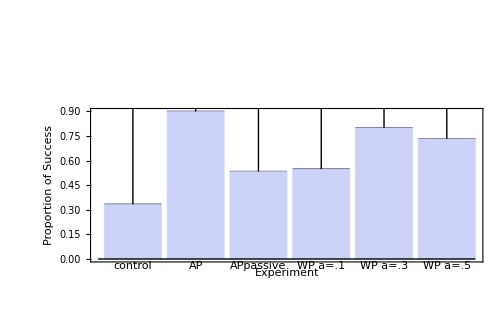

```mathematica
barChartWithSEM[{1/3,0.9,0.5333,0.5484,0.8,0.7333},{0,0.,0.,0.,0.,0.},(*myAxesLabel[{"Experiment", "Proportion of Success"}],*)pairwiseLabels->Map[Function[{record}, MapAt[Style[#,Large]&, record, 4]],{{2,3,1.05,"**",0.025},{1,2,1.2,"***",0.01},{2,4,1.3,"**",0.025},{1,5,1.5,"***"},{1,6,1.8,"**"}}],PlotRangePadding->{Automatic,{0,1}},ChartLabels->{"control","AP","APpassive","WP a=.1","WP a=.3","WP a=.5"}, AxesLabel -> None(*{"Experiment","Prop. of Success"}*), FrameLabel -> {"Experiment", "Proportion of Success"}, Frame -> {{True, False}, {True, False}}, 
FrameTicks -> {False, Automatic}, 
RotateLabel -> True]
```